# Clase G - Mediciones

## Dump

Pruebas:

- Polarizacion
- Ganancia de tension
- Sensibilidad
- Potencia de salida
- Ancho de banda: a 100mV. Barro hasta ver arriba y abajo cuando cae en 3dB, con grador y oscilo
- Slew rate: le meto una cuadrada de 500mV
- Impedancia de entrada: frecs 100, 1k, 10k. Nah, sin carga, 500mV
- Impedancia de salida: Ver con oscilo como baja con carga conocida. foto
- Distorsion: a 100, 1k, 10k, a 1w y 100w. Lo tengo que traducir a dB relativo 
- Intermodulacion: ver el efecto, no se bien como se mide. Meterle frecs de 1k y 1k3Hz	
- Rechazo de riple

```mathematica
20/8.
```

2.5

```mathematica
0.3 8
```

2.4

```mathematica
18.7/0.22
```

85.

```mathematica
20/Sqrt[2]/8.
```

1.76777

## Pasos para hoy

## General

```mathematica
SetDirectory["C:\\CUBASE\\Test proj\\Audio"];
potAInputPico[pot_]:=Sqrt[2]/40 potAOutputPico[pot]
potAOutputRMS[pot_]:=Sqrt[pot 8]
potAOutputPico[pot_]:=potAOutputRMS[pot]*Sqrt[2]
sr=48000;
vpico[db_]:=1.5 10^(db/20)
vdb[pico_]:=-3.52183+8.68589 Log[pico]
```

```mathematica
1/8/Sqrt[2]//N
```

0.0883883

```mathematica
0.2 0.22
```

0.044

## Polarizacion

El multiplicador de Vbe se coloca en la tension que genera una corriente de 200mA, medida a traves de la caida por la resistencia de emisor

```mathematica
0.0095/0.22
```

0.0431818

La salida sin entrada es de 4mV

```mathematica
Gana
```

## Ganancia

```mathematica
A
```

A entrada de 200mV pico pico de entrada. Salida, 4.96V pico pico, 195Hz

```mathematica
ganancia195=4.96/0.2;
```

24.8

A entrada de 206mV pico pico de entrada. Salida, 4.96V pico pico, 195Hz

```mathematica
ganancia1k=4.96/0.206;
```

```mathematica
ganancia1k
```

24.0777

```mathematica
40/Sqrt[2.]
```

28.2843

## Resistencia de entrada

Todas a 100mV pico

### A 100Hz

14kOhms.

### A 1kHz

14kOhms.

### A 10kHz

10kOhms.

## Resistencia de salida

Todas a 100mV pico

```mathematica
8/(8+rout)==r
```

### A 100Hz

Salida 4.48V pico pico sin carga
Con carga de 8, 4.68V

### A 1kHz

Salida 4.48V pico pico sin carga
Con carga de 8, 4.44V

### A 10kHz

Salida 4.48V pico pico sin carga
Con carga de 8, 4.36

## Ancho de banda

El ancho de banda medido a 3dB va de 6.6Hz hasta 225kHz. 
La senial de salida era de 2.12V a la salida, o entrada de 85mV

## Slew Rate

## THD

### A 2mW

```mathematica
(vin 40/Sqrt[2])^2/2/8
```

0.00195313

```mathematica
vin=0.00625;
```

```mathematica
potAInputPico[vin]
```

0.0111803

```mathematica
vdb[vin]
```

-47.6042

```mathematica
CopyFile["Audio 01_41.wav",FileNameJoin[{NotebookDirectory[],"thd-2mW.wav"}]];
```

```mathematica
dat=AudioData[Import["Audio 01_31.wav"]][[1]];
```

```mathematica
dat=dat~Drop~Round[sr 3.719];
```

```mathematica
freqs={125,250,500,1000,2000,4000,8000};
samples=Range[1,Length@dat,Round[10 sr]][[2;;8]];
```

```mathematica
dats=samples//Map[{#-10,#+10}&]//Flatten//Prepend[1]//Partition[#,2]&//Map[Take[dat,#]&];
```

```mathematica
Spectrogram[dat, 512,256,SampleRate->sr, FrameTicks->{Range[0,80,5], Automatic}]
```

```mathematica
Length@samples
```

10

```mathematica
fs=TimeSeries[Abs@Fourier[#], {0, 48000}]&/@dats;
```

```mathematica
ListLinePlot[dat[[samples[[10]]-20;;samples[[10]]+20]]]
```

```mathematica
TabView
```

```mathematica
TabView[Quantity[freqs[[;;3]],"Hertz"]->(ListLinePlot[20 Log10@TimeSeriesWindow[#, {0, 2000}]//alignMax, PlotRange->Full]&/@fs[[;;3]])//Thread]
```

123

```mathematica
TabView[Quantity[freqs[[4;;]],"Hertz"]->(ListLinePlot[20 Log10@TimeSeriesWindow[#, {0, 24000}]//alignMax, PlotRange->Full]&/@fs[[4;;]])//Thread]
```

1234

### A 1W

```mathematica
pot=1;
vrms=Sqrt[pot 8.];
vvpico=vrms Sqrt[2];
vin=vvpico/40 Sqrt[2]//N;
```

```mathematica
vin
```

0.141421

```mathematica
potAInputPico[vin]
```

0.053183

```mathematica
vdb[vin]
```

-20.5115

```mathematica
CopyFile["Audio 01_44.wav",FileNameJoin[{NotebookDirectory[],"thd-1W.wav"}]];
```

```mathematica
dat=AudioData[Import["Audio 01_44.wav"]][[1]];
```

```mathematica
dat=dat~Drop~Round[sr 3.719];
```

```mathematica
freqs={125,250,500,1000,2000,4000,8000};
samples=Range[1,Length@dat,Round[10 sr]][[2;;8]];
```

```mathematica
dats=samples//Map[{#-10,#+10}&]//Flatten//Prepend[1]//Partition[#,2]&//Map[Take[dat,#]&];
```

```mathematica
Spectrogram[dat, 512,256,SampleRate->sr, FrameTicks->{Range[0,80,5], Automatic}]
```

```mathematica
Length@samples
```

10

```mathematica
fs=TimeSeries[Abs@Fourier[#], {0, 48000}]&/@dats;
```

```mathematica
ListLinePlot[dat[[samples[[10]]-20;;samples[[10]]+20]]]
```

```mathematica
TabView
```

```mathematica
TabView[Quantity[freqs[[;;3]],"Hertz"]->(ListLinePlot[20 Log10@TimeSeriesWindow[#, {0, 2000}]//alignMax, PlotRange->Full]&/@fs[[;;3]])//Thread]
```

```mathematica
TabView[Quantity[freqs[[4;;]],"Hertz"]->(ListLinePlot[20 Log10@TimeSeriesWindow[#, {0, 24000}]//alignMax, PlotRange->Full]&/@fs[[4;;]])//Thread]
```

### A 10W

```mathematica
pot=10;
vrms=Sqrt[pot 8.];
vvpico=vrms Sqrt[2];
vin=vvpico/40 Sqrt[2]//N;
```

```mathematica
vin
```

0.447214

```mathematica
potAInputPico[vin]
```

0.0945742

```mathematica
vdb[vin]
```

-10.5115

```mathematica
CopyFile["Audio 01_43.wav",FileNameJoin[{NotebookDirectory[],"thd-10w.wav"}]];
```

```mathematica
dat=AudioData[Import["Audio 01_43.wav"]][[1]];
```

```mathematica
Spectrogram[Import["Audio 01_43.wav"]]
```

-Graphics-

```mathematica
AudioData
```

```mathematica
Spect
```

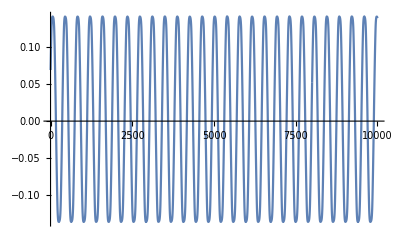

```mathematica
ListLinePlot[dat~Take~{10000,},PlotRange->Full]
```

```mathematica
dat=dat~Drop~Round[sr 3.719];
```

```mathematica
freqs={125,250,500,1000,2000,4000,8000};
samples=Range[1,Length@dat,Round[10 sr]][[2;;8]];
```

```mathematica
dats=samples//Map[{#-10,#+10}&]//Flatten//Prepend[1]//Partition[#,2]&//Map[Take[dat,#]&];
```

```mathematica
Spectrogram[dat, 512,256,SampleRate->sr, FrameTicks->{Range[0,80,5], Automatic}]
```

```mathematica
Length@samples
```

10

```mathematica
fs=TimeSeries[Abs@Fourier[#], {0, 48000}]&/@dats;
```

```mathematica
ListLinePlot[dat[[samples[[10]]-20;;samples[[10]]+20]]]
```

```mathematica
TabView
```

```mathematica
TabView[Quantity[freqs[[;;3]],"Hertz"]->(ListLinePlot[20 Log10@TimeSeriesWindow[#, {0, 2000}]//alignMax, PlotRange->Full]&/@fs[[;;3]])//Thread]
```

```mathematica
TabView[Quantity[freqs[[4;;]],"Hertz"]->(ListLinePlot[20 Log10@TimeSeriesWindow[#, {0, 24000}]//alignMax, PlotRange->Full]&/@fs[[4;;]])//Thread]
```

### A 100W

```mathematica
vrms=1/8.;
vvpico=vrms Sqrt[2];
vin=vvpico/40 Sqrt[2]//N;
```

```mathematica
vin
```

0.00625

```mathematica
potAInputPico[vin]
```

0.0111803

```mathematica
vdb[vin]
```

-47.6042

```mathematica
dat=AudioData[Import["Audio 01_31.wav"]][[1]];
```

```mathematica
dat=dat~Drop~Round[sr 3.719];
```

```mathematica
freqs={125,250,500,1000,2000,4000,8000};
samples=Range[1,Length@dat,Round[10 sr]][[2;;8]];
```

```mathematica
dats=samples//Map[{#-10,#+10}&]//Flatten//Prepend[1]//Partition[#,2]&//Map[Take[dat,#]&];
```

```mathematica
Spectrogram[dat, 512,256,SampleRate->sr, FrameTicks->{Range[0,80,5], Automatic}]
```

```mathematica
Length@samples
```

10

```mathematica
fs=TimeSeries[Abs@Fourier[#], {0, 48000}]&/@dats;
```

```mathematica
ListLinePlot[dat[[samples[[10]]-20;;samples[[10]]+20]]]
```

```mathematica
TabView
```

```mathematica
TabView[Quantity[freqs[[;;3]],"Hertz"]->(ListLinePlot[20 Log10@TimeSeriesWindow[#, {0, 2000}]//alignMax, PlotRange->Full]&/@fs[[;;3]])//Thread]
```

```mathematica
TabView[Quantity[freqs[[4;;]],"Hertz"]->(ListLinePlot[20 Log10@TimeSeriesWindow[#, {0, 24000}]//alignMax, PlotRange->Full]&/@fs[[4;;]])//Thread]
```

## Intermodulacion

```mathematica
aud=Import["C:\\CUBASE\\Test proj\\Audio\\Audio 01_19.wav"];
```

```mathematica
dat=AudioData[aud][[1]];
```

```mathematica
f=TimeSeries[Abs@Fourier[dat], {0, 48000}];
```

```mathematica
alignMax[l_]:=l-Max[l];
```

```mathematica
ListLinePlot[20 Log10@TimeSeriesWindow[f, {0, 400}]//alignMax, PlotRange->Full]
```

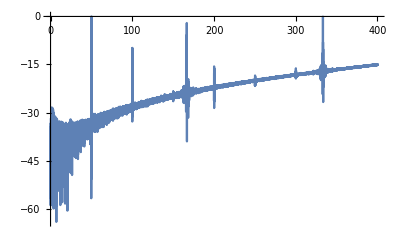

O sea, 0dB aca es aprox 1.5V pico de salida. Cada 20dB es dividir por 10 supongo.

```mathematica
1.5 10^(db/20)==vpico//Solve
```

{{db→-3.52183+8.68589 Log[vpico]}}

```mathematica
potAOutputPico[100.]
```

40.

```mathematica
potAInputPico[1]//vdb
```

-20.5115

```mathematica
potAInputPico[1]//N
```

0.141421

```mathematica
8/0.3
```

26.6667

```mathematica
70./1000
```

0.07

```mathematica
0.07^2 30
```

0.147

```mathematica
Audio
```

```mathematica
Play[0.05 Sin[2 Pi 440 t], {t, 0, 20}, PlayRange->{-1,1}, SampleRate->48000, SampleDepth->24]
```

-Graphics-

```mathematica
$DefaultAudioInputDevice
```

Line 1/2 (2- M-Audio Fast Track

```mathematica
ac=AudioCapture[SampleRate->48000];
```

```mathematica
AudioGenerator[{"Sin", 1000}, 10, "Real", SampleRate->48000]
```

```mathematica
ac
```

```mathematica
Import["
```

```mathematica
aud=;
```

```mathematica
Head[aud]
```

Audio

```mathematica
dat=AudioData[aud][[1]];
```

```mathematica
dat//Dimensions
```

{606208}

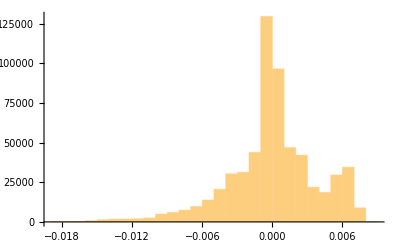

```mathematica
Histogram[dat]
```

```mathematica
MinMax[dat]
```

{-0.0181274,0.00842285}

```mathematica
fou=TimeSeries[Abs[Fourier[dat, FourierParameters->{1,-1}]], {0, 48000.}];
```

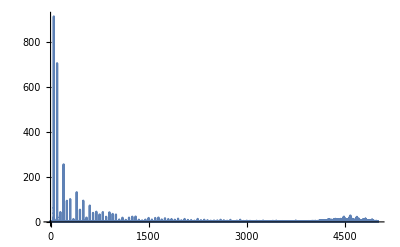

```mathematica
ListLinePlot[TimeSeriesWindow[ fou, {0, 5000}], PlotRange->Full]
```

```mathematica
ListLinePlot[fou]
```

$Aborted

```mathematica
ListLinePlot[, PlotRange->Full, DataRange->{0, 48000}]
```

-Graphics-

## Yeah

```mathematica
dat=Import["Audio 01_25.wav","WAV"]//AudioData//First;
```

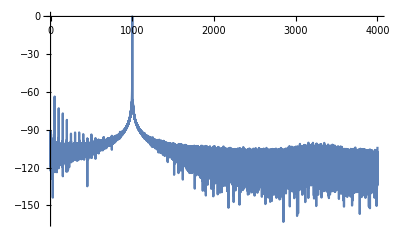

```mathematica
ListLinePlot[20 Log10@TimeSeriesWindow[f, {0, 4000}]//alignMax, PlotRange->Full]
```

```mathematica
dat
```

```mathematica
Directory[]
```

C:\CUBASE\Test proj\Audio

```mathematica
dat//Dimensions
```

{1,1433180}